```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
nodes[order_,coords_]:=Block[{xa,xb,newcoords},
xa=coords[[1]];
xb=coords[[2]];
newcoords=Table[xa+(1-i)(xa-xb)/order,{i,1,order+1}];
newcoords
]
```

```mathematica
ComputeShape[order_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],x],{i,1,n}];
ListPoli[npoints]
]
```

```mathematica
poli3[1,4]
```

poli3[1,4]

```mathematica
InterpolatingPolynomial[{{0,0},{0.5,1},{1,0}},x]
InterpolatingPolynomial[{{0,1},{0.5,0},{1,0}},x]
InterpolatingPolynomial[{{0,0},{0.5,0},{1,1}},x]
```

-4. (-1+x) x

(-1+x) (-1+2. x)

1+(-1+x) (1+2. x)

```mathematica
Table[InterpolatingPolynomial[co[[i]],x],{i,1,Length[co]}]
```

{}

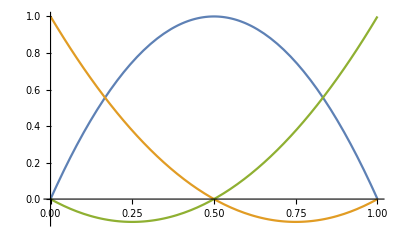

```mathematica
shape=Table[ComputeShape[order],{order,3,3}];
Plot[{InterpolatingPolynomial[{{0,0},{0.5,1},{1,0}},x],
InterpolatingPolynomial[{{0,1},{0.5,0},{1,0}},x],
InterpolatingPolynomial[{{0,0},{0.5,0},{1,1}},x]},{x,0,1}]
```

```mathematica
ComputeData[coords_,order_]:=Block[{J,PHI,DPHI,x,xx,D2PHI},
PHI=ComputeShape[order];
DPHI=Table[D[PHI[[i]],x],{i,1,Length[PHI]}];
D2PHI=Table[D[DPHI[[i]],x],{i,1,Length[DPHI]}];
xx=Sum[PHI[[i]] coords[[i]],{i,1,Length[PHI]}];
J=D[xx,x];

{PHI,DPHI,D2PHI,J,xx}
]
```

```mathematica
ComputeData[{{0,0}},1]
```

Part::partw: Part 2 of {{0,0}} does not exist.

{{1+1/2 (-1-x),(1+x)/2},{-1/2,1/2},{0,0},{1/2 {{0,0}}⟦2⟧,1/2 {{0,0}}⟦2⟧},{1/2 (1+x) {{0,0}}⟦2⟧,1/2 (1+x) {{0,0}}⟦2⟧}}

```mathematica
{phi,dphi,d2phi,J,xx}=ComputeData[{{0,0},{0.25,0},{0.75,0},{1,0}},1]
```

{{1+1/2 (-1-x),(1+x)/2},{-1/2,1/2},{0,0},{0.125,0},{0.125 (1+x),0}}

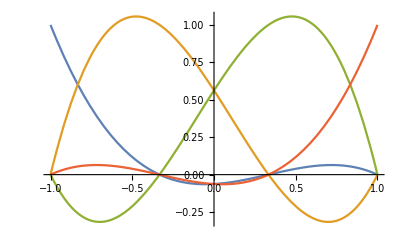

```mathematica
Plot[shape,{x,-1,1}]
```

```mathematica
ComputeData[xi_,coords_,order_]:=Block[{J,PHI,DPHI,x,xx,D2PHI},
PHI=ComputeShape[order];
DPHI=Table[D[PHI[[i]],x],{i,1,Length[PHI]}];
D2PHI=Table[D[DPHI[[i]],x],{i,1,Length[DPHI]}];
xx=Sum[PHI[[i]] coords[[i]],{i,1,Length[PHI]}];
J=D[xx,x];
{PHI,DPHI,D2PHI,J,xx}/.x->xi
]
```

```mathematica
ElementCalculations[order_,coords_,forcing_]:=Block[{Dphi,J,ip,vecPtosPesos,xi,w,Dpsi,D2psi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j},

vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
nnodes=Length[coords];
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];
Dx=Table[0,{nnodes}]
For[ip=1,ip≤ Length[vecPtosPesos],ip++,
xi=vecPtosPesos[[ip,1]];
w=vecPtosPesos[[ip,2]];
{psi,Dpsi,D2psi,J,x}=ComputeData[xi,coords,order];
Dphi=Table[(1/J)Dpsi[[i]] ,{i,1,Length[Dpsi]}];
For[i=1,i≤Length[ek],i++,
ef[[i]]+= d (forcing)psi[[i]]   w J ;
For[j=1,j≤ Length[ek],j++,
ek[[i,j]]+= (a Dphi[[i]]Dphi[[j]]+b Dphi[[j]] psi[[i]] +c psi[[i]]  psi[[j]]) J  w;
];
];
];

{ek  ,ef }
]
```

```mathematica
ElementCalculations2[order_,coords_,forcing_]:=Block[{Dphi,J,ip,vecPtosPesos,xi,w,Dpsi,D2psi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,D2phi},

vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
nnodes=Length[coords];
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];
Dx=Table[0,{nnodes}]
For[ip=1,ip≤ Length[vecPtosPesos],ip++,
xi=vecPtosPesos[[ip,1]];
w=vecPtosPesos[[ip,2]];
{psi,Dpsi,D2psi,J,x}=ComputeData[xi,coords,order];
Dphi=Table[(1/J)Dpsi[[i]] ,{i,1,Length[Dpsi]}];
D2phi=Table[(1/J)D2psi[[i]] ,{i,1,Length[D2psi]}];
For[i=1,i≤Length[ek],i++,
ef[[i]]+= d (forcing)psi[[i]]   w J;
For[j=1,j≤ Length[ek],j++,
ek[[i,j]]+= (a D2phi[[i]]D2phi[[j]]) J  w;
];
];
];

{ek  ,ef }
]
```

```mathematica
Assemble[coords_,nels_,order_,forcing_]:=Block[{i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},
sz=nels*order+1;
rows=order+1;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
rowglob=1;
colglob=1;


For[k=1,k≤nels,k++,

co=nodes[order,{coords[[k]],coords[[k+1]]}];
(*Print["co = ",co];
Print["coords = ",coords];*)
{Ke,Fe}=ElementCalculations[order,co,forcing];
ik=(k-1)*order;
For[i=1,i≤rows,i++,
For[j=1,j≤cols,j++,
Kglob[[ik+i,ik+j]]+=Ke[[i,j]];
];
Fglob[[ik+i]]+=Fe[[i]];
];
];

Kglob[[1,1]]=10^13;
Kglob[[nels*order+1,nels*order+1]]=10^13;

{Kglob,Fglob}
]
```

```mathematica
Assemble2[coords_,nels_,order_,forcing_]:=Block[{i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},
sz=nels*order+1;
rows=order+1;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
rowglob=1;
colglob=1;


For[k=1,k≤nels,k++,

co=nodes[order,{coords[[k]],coords[[k+1]]}];
(*Print["co = ",co];
Print["coords = ",coords];*)
{Ke,Fe}=ElementCalculations2[order,co,forcing];
ik=(k-1)*order;
For[i=1,i≤rows,i++,
For[j=1,j≤cols,j++,
Kglob[[ik+i,ik+j]]+=Ke[[i,j]];
];
Fglob[[ik+i]]+=Fe[[i]];
];
];

(* Dirichlet Boundary Conditions *)
For[  i=1,i<=nels*order+1,i++,
	Kglob[[1,i]]=0;
	Kglob[[nels*order+1,i]]=0;
	Kglob[[i,1]]=0;
	Kglob[[i,nels*order+1]]=0;
    ];
Kglob[[1,1]]=1;Kglob[[nels*order+1,nels*order+1]]=1;
Fglob[[1]]=0;Fglob[[nels*order+1]]=0;
(*Print[" K =",Kglob//MatrixForm];
Print[" f =",Fglob//MatrixForm];*)
{Kglob,Fglob}
]
```

```mathematica
Sol[nels_,order_,alpha_]:=Block[{k,i,phi,sol=0.},
For[k=1,k≤Length[alpha],k++,
phi=ComputeShape[order];

For[i=1,i≤Length[phi],i++,
sol+=phi[[i]] alpha[[k]] D[phi[[i]],x];
Print["phi[[i]] = ",phi[[i]]];
Print["alpha[[k]] = ",alpha[[k]]];
];
];
sol
]
```

```mathematica
phi={x/0.16667,1-x/0.16667};
```

```mathematica
1/6.
```

0.166667

```mathematica
coords
```

coords

```mathematica
7==Odd
```

7==Odd

```mathematica
If[OddQ[7],0,1]
```

0

```mathematica
psts=Table[{{coords[[i]],If[OddQ[i],0,1]},{coords[[i+1]],If[EvenQ[i],0,1]}},{i,1,Length[coords]-1}]
Table[psts[[i]]]
```

{}

Part::pkspec1: The expression i cannot be used as a part specification.

{}⟦i⟧

```mathematica
fs1=Table[InterpolatingPolynomial[{{coords[[i]],If[OddQ[i],0,1]},{coords[[i+1]],If[EvenQ[i],0,1]}},x],{i,1,Length[coords]-1}]
fs2=Table[InterpolatingPolynomial[{{coords[[i]],If[EvenQ[i],0,1]},{coords[[i+1]],If[OddQ[i],0,1]}},x],{i,1,Length[coords]-1}]
funcs=Table[{fs1[[i]],fs2[[i]]},{i,1,Length[fs2]}]
```

{}

{}

{}

```mathematica
x<=1/6,funcs[[1]][[2]],funcs[[2]][[1]]
```

```mathematica
Plot[funcs[[1]],{x,0,0.16667}]
Plot[funcs[[2]],{x,0.16667,1/3}]
```

Part::partw: Part 1 of {} does not exist.

-Graphics-

Part::partw: Part 2 of {} does not exist.

-Graphics-

```mathematica
(*co=nodes[1,{0,0.25}]
phi=ComputeShape[1]
xx=Sum[phi[[i]] co[[i]],{i,1,Length[phi]}](*x(ξ)*)
Table[xx,{x,-1,1,0.2}]
D[xx,x]
phi=ComputeShape[1] D[xx,x]
Plot[phi,{x,-1,1}]*)
```

```mathematica
ComputeSol[coords_,nels_,order_,alpha_]:=Block[{k,i,phi,sol=0.,xx,J,co,h,x},
phi=ComputeShape[order];
For[k=1,k≤nels,k++,
h=coords[[k]]-coords[[k+1]];
co=nodes[order,{coords[[k]],coords[[k+1]]}];
xx=Sum[phi[[i]] co[[i]],{i,1,Length[phi]}];
J=D[xx,x];
Print[J//N];
For[i=1,i≤Length[phi],i++,
sol+=phi[[i]] alpha[[k]] J;
(*Print["phi[[i]] = ",phi[[i]]];
Print["alpha[[k]] = ",alpha[[k]]];*)
];
];
sol
]
```

```mathematica
ComputeError[coord_,Solution_,exactsol_]:=Block[{x,i,e,vecPtosPesos},
vecPtosPesos=GaussianQuadratureWeights[10,-1,1];
e=Table[0,{Length[vecPtosPesos]}];
For[i=1,i≤ Length[coord],i++,
e[[i]]={coord[[i]],(exactsol/.x->coord[[i]]) - Solution[[i]]};
];
Interpolation[e]
]
```

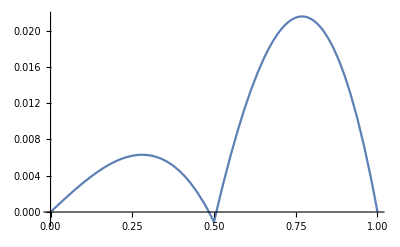
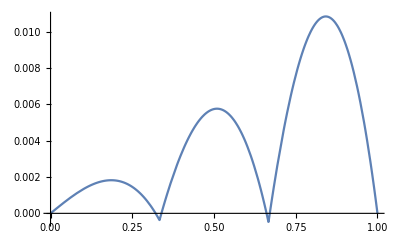
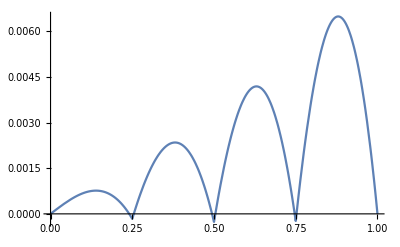
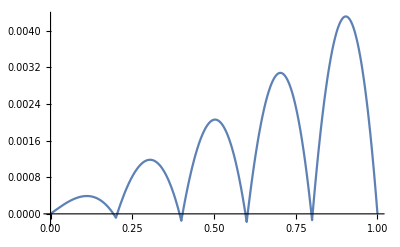
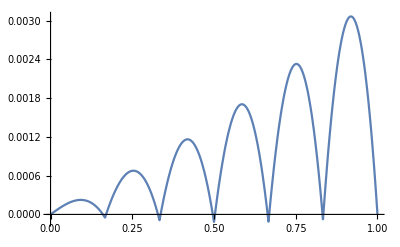

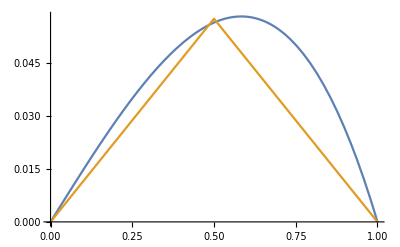
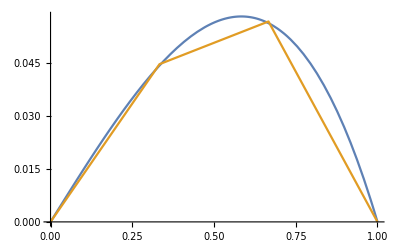
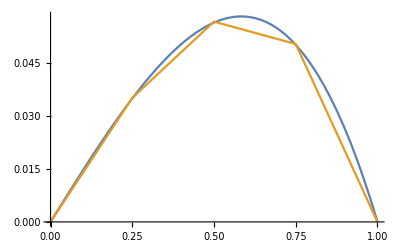

1.0179

0.505813

```mathematica
errovec={};
errovec2={};
errofuncs={};
For[i=2,i≤6,i++,
h=i;
p=1;
a=1;
b=0;
c=1;
d=1;
xa=0;
xb=1;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,x];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
(*s=Sol[coords,h,p,ceofs];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u[x]-x==0,u[0]==0,u[1]==0},u[x],x][[1,1,2]];

errox[xx_]:=(Exata/.x->xx)-xalfa[xx];
pl=Plot[Exata,{x,xa,xb},PlotRange->All];
Show[lp2,pl,PlotRange->All];
Plot[errox[x],{x,0,1}];
AppendTo[errovec,{Log[h]//N,-Log[Sqrt[NIntegrate[D[errox[x],x]^2+errox[x]^2,{x,xa,xb}]]]}];
AppendTo[errovec2,{Log[h]//N,-Log[Sqrt[NIntegrate[errox[x]^2,{x,xa,xb}]]]}];
AppendTo[errofuncs,xalfa];
];
Table[Plot[Exata-errofuncs[[i]][x],{x,xa,xb}],{i,1,Length[errofuncs]}]
Table[Plot[{Exata,errofuncs[[i]][x]},{x,xa,xb}],{i,1,Length[errofuncs]}]
ListLinePlot[{errovec,errovec2},AspectRatio->1.]
(Last[errovec][[1]]-First[errovec][[1]])/(Last[errovec][[2]]-First[errovec][[2]])
(Last[errovec2][[1]]-First[errovec2][[1]])/(Last[errovec2][[2]]-First[errovec2][[2]])
```

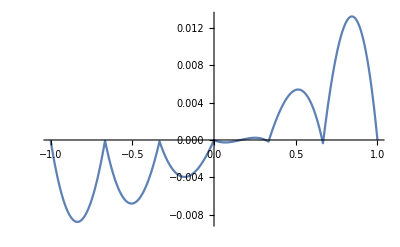
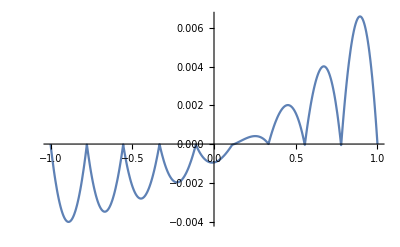
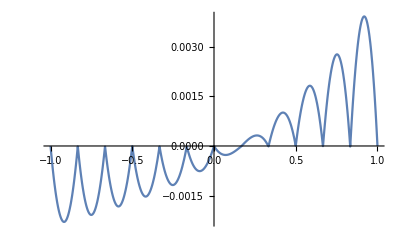
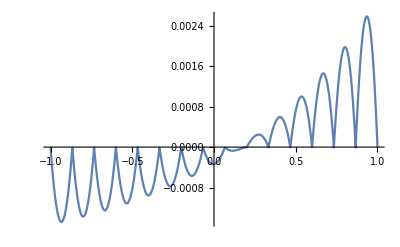
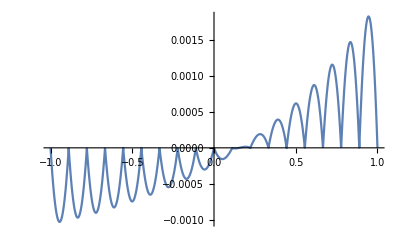

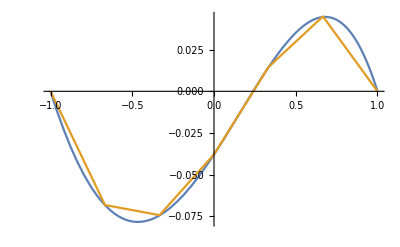
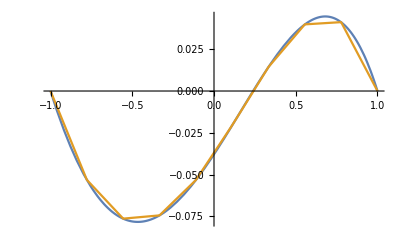
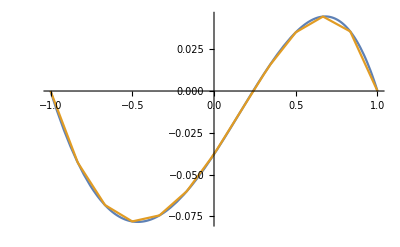

1.00982

0.506152

```mathematica
errovec={};
errovec2={};
errofuncs={};
For[i=2,i≤6,i++,
h=i;
p=3;
xa=-1;
xb=1.;
a=1;
b=1;
c=0;
d=1.;
Clear[coords];
Clear[ceofs];
coords=Table[delta,{delta,xa,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,x];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u'[x]-x==0,u[-1]==0,u[1]==0},u[x],x][[1,1,2]];
pl=Plot[Exata,{x,xa,xb},PlotRange->All,PlotStyle->Red];
Show[lp2,pl,PlotRange->All];
Plot[errox[x],{x,0,1}];
AppendTo[errovec,{Log[h]//N,-Log[Sqrt[NIntegrate[D[errox[x],x]^2+errox[x]^2,{x,xa,xb}]]]}];
AppendTo[errovec2,{Log[h]//N,-Log[Sqrt[NIntegrate[errox[x]^2,{x,xa,xb}]]]}];
AppendTo[errofuncs,xalfa];
];
Table[Plot[Exata-errofuncs[[i]][x],{x,xa,xb}],{i,1,Length[errofuncs]}]
Table[Plot[{Exata,errofuncs[[i]][x]},{x,xa,xb}],{i,1,Length[errofuncs]}]
ListLinePlot[{errovec,errovec2},AspectRatio->1.]
(Last[errovec][[1]]-First[errovec][[1]])/(Last[errovec][[2]]-First[errovec][[2]])
(Last[errovec2][[1]]-First[errovec2][[1]])/(Last[errovec2][[2]]-First[errovec2][[2]])
```

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

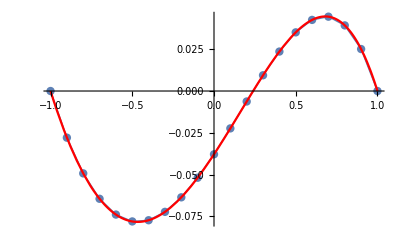

```mathematica
h=10;
p=2;
xa=-1;
xb=1.;
a=1;
b=1;
c=0;
d=1.;
Clear[coords];
Clear[ceofs];
coords=Table[delta,{delta,xa,xb,(xb-xa)/h}]
{k,f}=Assemble[coords,h,p,x];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u'[x]-x==0,u[-1]==0,u[1]==0},u[x],x][[1,1,2]];
pl=Plot[Exata,{x,xa,xb},PlotRange->All,PlotStyle->Red];
Show[lp2,pl,PlotRange->All]
```

{-1.,-0.98,-0.96,-0.94,-0.92,-0.9,-0.88,-0.86,-0.84,-0.82,-0.8,-0.78,-0.76,-0.74,-0.72,-0.7,-0.68,-0.66,-0.64,-0.62,-0.6,-0.58,-0.56,-0.54,-0.52,-0.5,-0.48,-0.46,-0.44,-0.42,-0.4,-0.38,-0.36,-0.34,-0.32,-0.3,-0.28,-0.26,-0.24,-0.22,-0.2,-0.18,-0.16,-0.14,-0.12,-0.1,-0.08,-0.06,-0.04,-0.02,0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.}

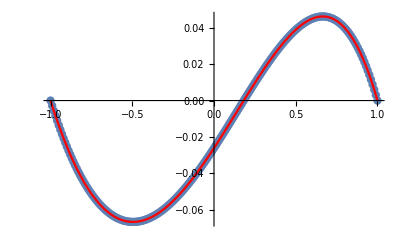

```mathematica
h=100;
p=2;
xa=-1;
xb=1.;
a=1;
b=1;
c=1;
d=1;
Clear[coords];
Clear[ceofs];
coords=Table[delta,{delta,xa,xb,(xb-xa)/h}]
{k,f}=Assemble[coords,h,p,x];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{- u''[x]+ u'[x]+ u[x]-x==0,u[-1]==0,u[1]==0},u[x],x][[1,1,2]];
plex=Plot[Exata,{x,-1,1},PlotStyle->Red];
Show[lp2,plex,PlotRange->All]
```

{0,1/30,1/15,1/10,2/15,1/6,1/5,7/30,4/15,3/10,1/3,11/30,2/5,13/30,7/15,1/2,8/15,17/30,3/5,19/30,2/3,7/10,11/15,23/30,4/5,5/6,13/15,9/10,14/15,29/30,1}

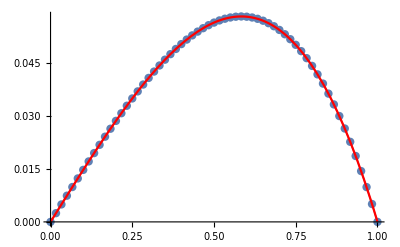

```mathematica
h=30;
p=2;
a=1;
b=0;
c=1;
d=1;
xa=0;
xb=1;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}]
{k,f}=Assemble[coords,h,p,x];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab=Table[{(i-1)/n,ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u[x]-x==0,u[0]==0,u[1]==0},u[x],x][[1,1,2]];
plex=Plot[Exata,{x,0,1},PlotStyle->Red];
Show[lp2,plex]
```

{0,π/12,π/6,π/4,π/3,(5 π)/12,π/2}

1/2 x Sin[2 x]

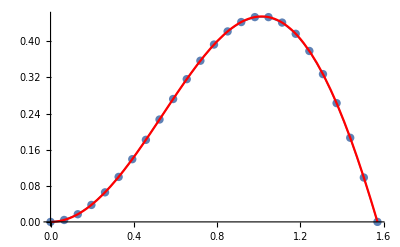

```mathematica
h=6;
p=4;
a=1;
b=0;
c=1;
d=1;
xa=0;
xb=Pi/2;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}]
forcing=-2 Cos[x]^2+5 x Cos[x] Sin[x]+2 Sin[x]^2;
{k,f}=Assemble[coords,h,p,forcing];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u[x]==forcing,u[0]==0,u[Pi/2]==0},u[x],x][[1,1,2]]
plex=Plot[Exata,{x,0,Pi/2},PlotStyle->Red];
Show[lp2,plex,PlotRange->All]
```

{0.,1.,2.,3.,4.,5.}

k = (10000000000000 | -4.725 | 1.35 | -0.325 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.725 | 10.8 | -7.425 | 1.35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.35 | -7.425 | 10.8 | -4.725 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.325 | 1.35 | -4.725 | 7.4 | -4.725 | 1.35 | -0.325 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -4.725 | 10.8 | -7.425 | 1.35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.35 | -7.425 | 10.8 | -4.725 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.325 | 1.35 | -4.725 | 7.4 | -4.725 | 1.35 | -0.325 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4.725 | 10.8 | -7.425 | 1.35 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.35 | -7.425 | 10.8 | -4.725 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.325 | 1.35 | -4.725 | 7.4 | -4.725 | 1.35 | -0.325 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.725 | 10.8 | -7.425 | 1.35 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.35 | -7.425 | 10.8 | -4.725 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.325 | 1.35 | -4.725 | 7.4 | -4.725 | 1.35 | -0.325
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.725 | 10.8 | -7.425 | 1.35
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.35 | -7.425 | 10.8 | -4.725
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.325 | 1.35 | -4.725 | 10000000000000)

f = (-0.50003
-0.00015
-0.00051
-0.000393333
-0.00069
-0.00087
-0.000593333
-0.00093
-0.00093
-0.000593333
-0.00087
-0.00069
-0.000393333
-0.00051
-0.00015
0.49997)

-0.00416667 x+0.000333333 x^3-0.0000333333 x^4

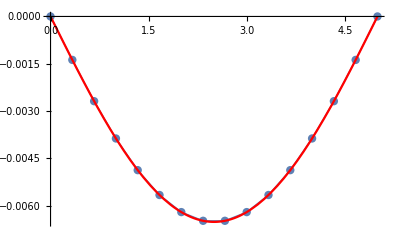

```mathematica
h=5;
p=3;
a=1;
b=0;
c=0;
d=1;
xa=0;
L=5.;
q=-8;
xb=L;
EI=10000;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}]
forcing=(-q x^2/2 + q L x/2)/EI;
{k,f}=Assemble[coords,h,p,forcing];
Print["k = ",k//MatrixForm]
Print["f = ",f//MatrixForm]
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{u''[x]==-forcing,u[0]==0,u[L]==0},u[x],x][[1,1,2]]
plex=Plot[Exata,{x,0,L},PlotStyle->Red];
Show[lp2,plex,PlotRange->All]
```

```mathematica
Clear[L]
p1=DSolve[{u''''[x]==0,u[0]==1,u'[0]==0,u[L]==0,u'[L]==0},u[x],x][[1,1,2]]
p2=DSolve[{u''''[x]==0,u[0]==0,u'[0]==1,u[L]==0,u'[L]==0},u[x],x][[1,1,2]]
p3=DSolve[{u''''[x]==0,u[0]==0,u'[0]==0,u[L]==1,u'[L]==0},u[x],x][[1,1,2]]
p4=DSolve[{u''''[x]==0,u[0]==0,u'[0]==0,u[L]==0,u'[L]==1},u[x],x][[1,1,2]]
shapes=Outer[Times,D[phi,x,x],D[phi,x,x]]
phi={p1,p2,p3,p4}
Clear[EI]
k=Table[EI Integrate[shapes[[i]],{x,0,L}],{i,1,Length[shapes]}]
k//MatrixForm
```

(L^3-3 L x^2+2 x^3)/L^3

(L^2 x-2 L x^2+x^3)/L^2

(3 L x^2-2 x^3)/L^3

(-L x^2+x^3)/L^2

{{0,0},{0,0}}

{(L^3-3 L x^2+2 x^3)/L^3,(L^2 x-2 L x^2+x^3)/L^2,(3 L x^2-2 x^3)/L^3,(-L x^2+x^3)/L^2}

{{0,0},{0,0}}

(0 | 0
0 | 0)

```mathematica
phi
```

{(L^3-3 L x^2+2 x^3)/L^3,(L^2 x-2 L x^2+x^3)/L^2,(3 L x^2-2 x^3)/L^3,(-L x^2+x^3)/L^2}

1

{0.,5.}

k = (1 | 0 | 0 | 0 | 0 | 0
0 | 346.199 | -486.018 | 389.013 | -188.973 | 0
0 | -486.018 | 775.422 | -714.224 | 389.013 | 0
0 | 389.013 | -714.224 | 775.422 | -486.018 | 0
0 | -188.973 | 389.013 | -486.018 | 346.199 | 0
0 | 0 | 0 | 0 | 0 | 1)

f = (0
-0.00104167
-0.000694444
-0.000694444
-0.00104167
0)

-0.00416667 x+0.000333333 x^3-0.0000333333 x^4

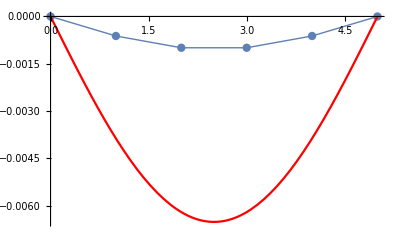

```mathematica
h=1
p=5;
a=1;
b=0;
c=0;
d=1;
xa=0;
L=5.;
q=-8;
xb=L;
EI=10000;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}]

forcing=q/EI;
{k,f}=Assemble2[coords,h,p,forcing];
Print["k = ",k//MatrixForm]
Print["f = ",f//MatrixForm]
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
forcing=(-q x^2/2 + q L x/2)/EI;
Exata=DSolve[{u''[x]==-forcing,u[0]==0,u[L]==0},u[x],x][[1,1,2]]
plex=Plot[Exata,{x,0,L},PlotStyle->Red];
Show[lp2,plex,PlotRange->All]
```

-Graphics-

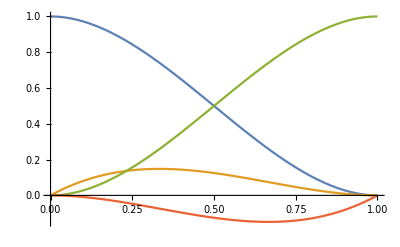

```mathematica
shape=ComputeShape[3];
Plot[shape,{x,-1,1}]
L=1;
Plot[phi,{x,0,1}]
```

```mathematica
shape//Expand
phi//Expand
```

{-1/16+x/16+(9 x^2)/16-(9 x^3)/16,9/16-(27 x)/16-(9 x^2)/16+(27 x^3)/16,9/16+(27 x)/16-(9 x^2)/16-(27 x^3)/16,-1/16-x/16+(9 x^2)/16+(9 x^3)/16}

{1-3 x^2+2 x^3,x-2 x^2+x^3,3 x^2-2 x^3,-x^2+x^3}

```mathematica
ElementCalculations[order_,coords_,forcing_]:=Block[{Dphi,J,ip,vecPtosPesos,xi,w,Dpsi,D2psi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j},

vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
nnodes=Length[coords];
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];
Dx=Table[0,{nnodes}];
For[ip=1,ip≤ Length[vecPtosPesos],ip++,
xi=vecPtosPesos[[ip,1]];
w=vecPtosPesos[[ip,2]];
{psi,Dpsi,D2psi,J,x}=ComputeData[xi,coords,order];
(*Print["Dpsi = ",Dpsi];*)
Dphi=Table[(1/J)Dpsi[[i]] ,{i,1,Length[Dpsi]}];
(*Print["Dphi = ",Dphi];*)
For[i=1,i≤Length[ek],i++,
ef[[i]]+= d (forcing)psi[[i]]   w J;
For[j=1,j≤ Length[ek],j++,
ek[[i,j]]+= (a Dphi[[i]]Dphi[[j]]+b Dphi[[j]] psi[[i]] +c psi[[i]]  psi[[j]]) J  w;
];
];
];

{ek  ,ef }
]
```

```mathematica
Assemble[coords_,nels_,order_,forcing_]:=Block[{kbc,fbc,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co,vecPtosPesos,nnodes,ip,xi,w,psi,Dpsi,D2psi,J,x},
sz=nels*order+1;
rows=order+1;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
rowglob=1;
colglob=1;
For[k=1,k≤nels,k++,
co=nodes[order,{coords[[k]],coords[[k+1]]}];
{Ke,Fe}=ElementCalculations[order,co,forcing];
ik=(k-1)*order;
For[i=1,i≤rows,i++,
For[j=1,j≤cols,j++,
Kglob[[ik+i,ik+j]]+=Ke[[i,j]];
];
Fglob[[ik+i]]+=Fe[[i]];
];
];

Kglob[[1,1]]*= 10^12;

{Kglob,Fglob}
]
```

(1.68×10^19 | -1.68×10^7 | 0 | 0 | 0
-1.68×10^7 | 3.36×10^7 | -1.68×10^7 | 0 | 0
0 | -1.68×10^7 | 3.36×10^7 | -1.68×10^7 | 0
0 | 0 | -1.68×10^7 | 3.36×10^7 | -1.68×10^7
0 | 0 | 0 | -1.68×10^7 | 1.68×10^7)

(0.125
0.25
0.25
0.25
0.125)

1.5873×10^-7 x-3.96825×10^-8 x^3

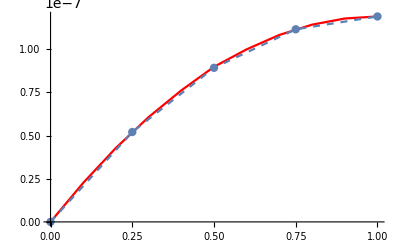

```mathematica
errovec={};
errovec2={};
errofuncs={};
Young = 2.1 10^8;
A=0.1 0.2;
h=4;
p=1;
a=Young A;
b=0;
c=0;
d=1;
xa=0;
xb=1;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,1];
k//MatrixForm
f//MatrixForm
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
n=h  p;
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->{Dashed}];
sftool={{1,1.190476 10^-7},{0.9,1.178571 10^-7},{0.8,1.142857 10^-7},{0.7,1.083333 10^-7},{0.6, 1 10^-7},{0.5, 8.98571 10^-8},{0.4,7.619047 10^-8},{0.3, 6.071428 10^-8},{0.2,4.285713 10^-8},{0.1,2.261904 10^-8},{0,0}};
plsftool=ListLinePlot[sftool,PlotStyle->{Red}];
Exata=DSolve[{-a u''[x]==x,u[0]==0,u[1]==1/(2 A Young)},u[x],x][[1,1,2]]
plex=Plot[Exata,{x,0,1},PlotStyle->Red];
(*plex=Plot[x^2/(2 Young A),{x,0,1},PlotStyle->Red];*)
Show[plsftool,lp2,PlotRange->All]
```